# Sex-ratio adjustment erodes sexual selection: numerical simulations

```mathematica
Clear["Global`*"]
```

## Define resident transition matrix and mate choice functions

Resident transition matrix, note that vm0 = 1

```mathematica
A=1/2 k{{((1-α)(1-s0)+α(1-s1))vf,q0(1-s0)vf,q1(1-s1)vf},{(1-α)s0(1-μ0)+α s1 μ1,q0 s0 (1-μ0),q1 s1 μ1},{((1-α)s0 μ0+α s1 (1-μ1))vm1,q0 s0 μ0 vm1,q1 s1 (1-μ1) vm1}};
```

```mathematica
A//MatrixForm
```

Probability attractive male is chosen by female with preference p:

```mathematica
α=r ym1/(ym0+r ym1)
```

(r ym1)/(ym0+r ym1)

Mating probability unattractive and attractive male:

```mathematica
q0=yf/(ym0+r ym1)
q1=yf r/(ym0+r ym1)
```

yf/(ym0+r ym1)

(r yf)/(ym0+r ym1)

Average sex ratio

```mathematica
sbar=(1-α)s0+α s1
```

(r s1 ym1)/(ym0+r ym1)+s0 (1-(r ym1)/(ym0+r ym1))

From eq. S2, we have λ=2a11 = k (1-sbar) vf. In a stable population, we thus have

```mathematica
k=1/((1-sbar)vf)
```

1/(vf (1-(r s1 ym1)/(ym0+r ym1)-s0 (1-(r ym1)/(ym0+r ym1))))

```mathematica
A//MatrixForm
```

(((r (1-s1) ym1)/(ym0+r ym1)+(1-s0) (1-(r ym1)/(ym0+r ym1)))/(2 (1-(r s1 ym1)/(ym0+r ym1)-s0 (1-(r ym1)/(ym0+r ym1)))) | ((1-s0) yf)/(2 (ym0+r ym1) (1-(r s1 ym1)/(ym0+r ym1)-s0 (1-(r ym1)/(ym0+r ym1)))) | (r (1-s1) yf)/(2 (ym0+r ym1) (1-(r s1 ym1)/(ym0+r ym1)-s0 (1-(r ym1)/(ym0+r ym1))))
(s0 (1-(r ym1)/(ym0+r ym1)) (1-μ0)+(r s1 ym1 μ1)/(ym0+r ym1))/(2 vf (1-(r s1 ym1)/(ym0+r ym1)-s0 (1-(r ym1)/(ym0+r ym1)))) | (s0 yf (1-μ0))/(2 vf (ym0+r ym1) (1-(r s1 ym1)/(ym0+r ym1)-s0 (1-(r ym1)/(ym0+r ym1)))) | (r s1 yf μ1)/(2 vf (ym0+r ym1) (1-(r s1 ym1)/(ym0+r ym1)-s0 (1-(r ym1)/(ym0+r ym1))))
(vm1 (s0 (1-(r ym1)/(ym0+r ym1)) μ0+(r s1 ym1 (1-μ1))/(ym0+r ym1)))/(2 vf (1-(r s1 ym1)/(ym0+r ym1)-s0 (1-(r ym1)/(ym0+r ym1)))) | (s0 vm1 yf μ0)/(2 vf (ym0+r ym1) (1-(r s1 ym1)/(ym0+r ym1)-s0 (1-(r ym1)/(ym0+r ym1)))) | (r s1 vm1 yf (1-μ1))/(2 vf (ym0+r ym1) (1-(r s1 ym1)/(ym0+r ym1)-s0 (1-(r ym1)/(ym0+r ym1)))))

## Solving for stable class frequencies yf, ym0, ym1

Specify equations for right eigenvector, where λ=1

```mathematica
yeqns={yf==A[[1,1]]yf+A[[1,2]]ym0+A[[1,3]]ym1,ym0==A[[2,1]]yf+A[[2,2]]ym0+A[[2,3]]ym1,
ym1==A[[3,1]]yf+A[[3,2]]ym0+A[[3,3]]ym1}
```

{yf==((1-s0) yf ym0)/(2 (ym0+r ym1) (1-(r s1 ym1)/(ym0+r ym1)-s0 (1-(r ym1)/(ym0+r ym1))))+(r (1-s1) yf ym1)/(2 (ym0+r ym1) (1-(r s1 ym1)/(ym0+r ym1)-s0 (1-(r ym1)/(ym0+r ym1))))+(yf ((r (1-s1) ym1)/(ym0+r ym1)+(1-s0) (1-(r ym1)/(ym0+r ym1))))/(2 (1-(r s1 ym1)/(ym0+r ym1)-s0 (1-(r ym1)/(ym0+r ym1)))),ym0==(s0 yf ym0 (1-μ0))/(2 vf (ym0+r ym1) (1-(r s1 ym1)/(ym0+r ym1)-s0 (1-(r ym1)/(ym0+r ym1))))+(r s1 yf ym1 μ1)/(2 vf (ym0+r ym1) (1-(r s1 ym1)/(ym0+r ym1)-s0 (1-(r ym1)/(ym0+r ym1))))+(yf (s0 (1-(r ym1)/(ym0+r ym1)) (1-μ0)+(r s1 ym1 μ1)/(ym0+r ym1)))/(2 vf (1-(r s1 ym1)/(ym0+r ym1)-s0 (1-(r ym1)/(ym0+r ym1)))),ym1==(s0 vm1 yf ym0 μ0)/(2 vf (ym0+r ym1) (1-(r s1 ym1)/(ym0+r ym1)-s0 (1-(r ym1)/(ym0+r ym1))))+(vm1 yf (s0 (1-(r ym1)/(ym0+r ym1)) μ0+(r s1 ym1 (1-μ1))/(ym0+r ym1)))/(2 vf (1-(r s1 ym1)/(ym0+r ym1)-s0 (1-(r ym1)/(ym0+r ym1))))+(r s1 vm1 yf ym1 (1-μ1))/(2 vf (ym0+r ym1) (1-(r s1 ym1)/(ym0+r ym1)-s0 (1-(r ym1)/(ym0+r ym1))))}

Solve for yf, ym0, ym1:

```mathematica
ysols=Solve[(yeqns[[2;;3]]/.yf->1-ym1-ym0//Simplify),{ym0,ym1}]//Simplify
```

{{ym0→(s0^2 (-1+μ0) (vf-vf μ0+s1 vf (-1+μ0+μ1)-s1 vm1 (-1+μ0+μ1))-s1 vf μ1 (r s1 vm1 (-1+μ1)+√(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1)))+s0 (s1 vf μ1-s1 vf μ0 μ1+vf √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))-s1 vf √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+s1 vm1 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))-vf μ0 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+s1 vf μ0 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))-s1 vm1 μ0 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+s1 vf μ1 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))-s1 vm1 μ1 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+r s1 vm1 (s1 (vm1 (-1+μ1)-2 μ1) (-1+μ0+μ1)+vf (1-μ1-μ0 (1+μ1)+s1 (1+μ1) (-1+μ0+μ1)))))/(2 (s0^2 (-1+vf+μ0-vm1 μ0) (vf-vf μ0+s1 vf (-1+μ0+μ1)-s1 vm1 (-1+μ0+μ1))+s1 vf (vf μ1+r vm1 (-1+μ1) ((-1+s1) vf+s1 vm1 (-1+μ1)-s1 μ1))-s0 (-r s1^2 vm1 (vm1 (-1+μ1)-μ1) (-1+μ0+μ1)+vf^2 (1+(-1+r vm1) μ0+r s1^2 vm1 (-1+μ0+μ1)+s1 (-1+μ0+2 μ1-r vm1 (-1+2 μ0+μ1)))+s1 vf ((-1+μ0) μ1+r vm1^2 (-1+μ1) (-μ0+s1 (-1+μ0+μ1))-vm1 (-1+μ0+μ1+μ0 μ1+r (1-μ1-μ0 (1+μ1)+s1 (1+μ1) (-1+μ0+μ1))))))),ym1→(vm1 (s0^2 vf (-1+μ0) μ0-s0^2 s1 (-1+vf+μ0+vf μ0-2 vm1 μ0) (-1+μ0+μ1)+s1 vf (-1+μ1) (r s1 vm1 (-1+μ1)+√(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1)))+s0 (-r s1^2 (-1+vf) vm1 (-1+μ1) (-1+μ0+μ1)+vf μ0 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+s1 ((-1+μ0+μ1) √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+vf μ0 (1+r vm1 (-1+μ1)+μ1-√(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1)))-vf (-1+μ1) (-1+√(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1)))))))/(2 (s0^2 (-1+vf+μ0-vm1 μ0) (vf-vf μ0+s1 vf (-1+μ0+μ1)-s1 vm1 (-1+μ0+μ1))+s1 vf (vf μ1+r vm1 (-1+μ1) ((-1+s1) vf+s1 vm1 (-1+μ1)-s1 μ1))-s0 (-r s1^2 vm1 (vm1 (-1+μ1)-μ1) (-1+μ0+μ1)+vf^2 (1+(-1+r vm1) μ0+r s1^2 vm1 (-1+μ0+μ1)+s1 (-1+μ0+2 μ1-r vm1 (-1+2 μ0+μ1)))+s1 vf ((-1+μ0) μ1+r vm1^2 (-1+μ1) (-μ0+s1 (-1+μ0+μ1))-vm1 (-1+μ0+μ1+μ0 μ1+r (1-μ1-μ0 (1+μ1)+s1 (1+μ1) (-1+μ0+μ1)))))))},{ym0→(s0^2 (-1+μ0) (vf-vf μ0+s1 vf (-1+μ0+μ1)-s1 vm1 (-1+μ0+μ1))+s1 vf μ1 (-r s1 vm1 (-1+μ1)+√(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1)))+s0 (s1 vf μ1-s1 vf μ0 μ1-vf √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+s1 vf √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))-s1 vm1 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+vf μ0 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))-s1 vf μ0 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+s1 vm1 μ0 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))-s1 vf μ1 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+s1 vm1 μ1 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+r s1 vm1 (s1 (vm1 (-1+μ1)-2 μ1) (-1+μ0+μ1)+vf (1-μ1-μ0 (1+μ1)+s1 (1+μ1) (-1+μ0+μ1)))))/(2 (s0^2 (-1+vf+μ0-vm1 μ0) (vf-vf μ0+s1 vf (-1+μ0+μ1)-s1 vm1 (-1+μ0+μ1))+s1 vf (vf μ1+r vm1 (-1+μ1) ((-1+s1) vf+s1 vm1 (-1+μ1)-s1 μ1))-s0 (-r s1^2 vm1 (vm1 (-1+μ1)-μ1) (-1+μ0+μ1)+vf^2 (1+(-1+r vm1) μ0+r s1^2 vm1 (-1+μ0+μ1)+s1 (-1+μ0+2 μ1-r vm1 (-1+2 μ0+μ1)))+s1 vf ((-1+μ0) μ1+r vm1^2 (-1+μ1) (-μ0+s1 (-1+μ0+μ1))-vm1 (-1+μ0+μ1+μ0 μ1+r (1-μ1-μ0 (1+μ1)+s1 (1+μ1) (-1+μ0+μ1))))))),ym1→(vm1 (s0^2 vf (-1+μ0) μ0-s0^2 s1 (-1+vf+μ0+vf μ0-2 vm1 μ0) (-1+μ0+μ1)-s1 vf (-1+μ1) (-r s1 vm1 (-1+μ1)+√(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1)))+s0 (-r s1^2 (-1+vf) vm1 (-1+μ1) (-1+μ0+μ1)-vf μ0 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+s1 (-(-1+μ0+μ1) √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+vf (-1+μ1) (1+√(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1)))+vf μ0 (1+r vm1 (-1+μ1)+μ1+√(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1)))))))/(2 (s0^2 (-1+vf+μ0-vm1 μ0) (vf-vf μ0+s1 vf (-1+μ0+μ1)-s1 vm1 (-1+μ0+μ1))+s1 vf (vf μ1+r vm1 (-1+μ1) ((-1+s1) vf+s1 vm1 (-1+μ1)-s1 μ1))-s0 (-r s1^2 vm1 (vm1 (-1+μ1)-μ1) (-1+μ0+μ1)+vf^2 (1+(-1+r vm1) μ0+r s1^2 vm1 (-1+μ0+μ1)+s1 (-1+μ0+2 μ1-r vm1 (-1+2 μ0+μ1)))+s1 vf ((-1+μ0) μ1+r vm1^2 (-1+μ1) (-μ0+s1 (-1+μ0+μ1))-vm1 (-1+μ0+μ1+μ0 μ1+r (1-μ1-μ0 (1+μ1)+s1 (1+μ1) (-1+μ0+μ1)))))))}}

```mathematica
yfreplace=yf->1-ym0-ym1/.ysols//Simplify
```

{yf→(vf (s0^2 ((-1+μ0) (1-2 vf+(-1+vm1) μ0)+s1 (-1+2 vf+μ0-vm1 (1+μ0)) (-1+μ0+μ1))+s1 (2 vf μ1+r vm1 (-1+μ1) (2 (-1+s1) vf+s1 vm1 (-1+μ1)-s1 μ1)+(vm1+μ1-vm1 μ1) √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1)))+s0 (-s1 vm1+r s1 vm1-r s1^2 vm1-r s1^2 vm1^2+s1 vm1 μ0-r s1 vm1 μ0+r s1^2 vm1 μ0-r s1 vm1^2 μ0+r s1^2 vm1^2 μ0+s1 μ1+s1 vm1 μ1-r s1 vm1 μ1+2 r s1^2 vm1^2 μ1-s1 μ0 μ1+s1 vm1 μ0 μ1-r s1 vm1 μ0 μ1+r s1^2 vm1 μ0 μ1+r s1 vm1^2 μ0 μ1-r s1^2 vm1^2 μ0 μ1+r s1^2 vm1 μ1^2-r s1^2 vm1^2 μ1^2-√(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+s1 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))-s1 vm1 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+μ0 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))-s1 μ0 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))-vm1 μ0 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+s1 vm1 μ0 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))-s1 μ1 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+s1 vm1 μ1 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))-2 vf (1-μ0+r vm1 μ0+r s1^2 vm1 (-1+μ0+μ1)+s1 (-1+μ0+2 μ1-r vm1 (-1+2 μ0+μ1))))))/(2 (s0^2 (-1+vf+μ0-vm1 μ0) (vf-vf μ0+s1 vf (-1+μ0+μ1)-s1 vm1 (-1+μ0+μ1))+s1 vf (vf μ1+r vm1 (-1+μ1) ((-1+s1) vf+s1 vm1 (-1+μ1)-s1 μ1))-s0 (-r s1^2 vm1 (vm1 (-1+μ1)-μ1) (-1+μ0+μ1)+vf^2 (1+(-1+r vm1) μ0+r s1^2 vm1 (-1+μ0+μ1)+s1 (-1+μ0+2 μ1-r vm1 (-1+2 μ0+μ1)))+s1 vf ((-1+μ0) μ1+r vm1^2 (-1+μ1) (-μ0+s1 (-1+μ0+μ1))-vm1 (-1+μ0+μ1+μ0 μ1+r (1-μ1-μ0 (1+μ1)+s1 (1+μ1) (-1+μ0+μ1))))))),yf→(vf (s0^2 ((-1+μ0) (1-2 vf+(-1+vm1) μ0)+s1 (-1+2 vf+μ0-vm1 (1+μ0)) (-1+μ0+μ1))+s1 (2 vf μ1+r vm1 (-1+μ1) (2 (-1+s1) vf+s1 vm1 (-1+μ1)-s1 μ1)+(vm1 (-1+μ1)-μ1) √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1)))+s0 (-s1 vm1+r s1 vm1-r s1^2 vm1-r s1^2 vm1^2+s1 vm1 μ0-r s1 vm1 μ0+r s1^2 vm1 μ0-r s1 vm1^2 μ0+r s1^2 vm1^2 μ0+s1 μ1+s1 vm1 μ1-r s1 vm1 μ1+2 r s1^2 vm1^2 μ1-s1 μ0 μ1+s1 vm1 μ0 μ1-r s1 vm1 μ0 μ1+r s1^2 vm1 μ0 μ1+r s1 vm1^2 μ0 μ1-r s1^2 vm1^2 μ0 μ1+r s1^2 vm1 μ1^2-r s1^2 vm1^2 μ1^2+√(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))-s1 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+s1 vm1 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))-μ0 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+s1 μ0 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+vm1 μ0 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))-s1 vm1 μ0 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))+s1 μ1 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))-s1 vm1 μ1 √(s0^2 (-1+μ0)^2+r^2 s1^2 vm1^2 (-1+μ1)^2+2 r s0 s1 vm1 (-1+μ0+μ1+μ0 μ1))-2 vf (1-μ0+r vm1 μ0+r s1^2 vm1 (-1+μ0+μ1)+s1 (-1+μ0+2 μ1-r vm1 (-1+2 μ0+μ1))))))/(2 (s0^2 (-1+vf+μ0-vm1 μ0) (vf-vf μ0+s1 vf (-1+μ0+μ1)-s1 vm1 (-1+μ0+μ1))+s1 vf (vf μ1+r vm1 (-1+μ1) ((-1+s1) vf+s1 vm1 (-1+μ1)-s1 μ1))-s0 (-r s1^2 vm1 (vm1 (-1+μ1)-μ1) (-1+μ0+μ1)+vf^2 (1+(-1+r vm1) μ0+r s1^2 vm1 (-1+μ0+μ1)+s1 (-1+μ0+2 μ1-r vm1 (-1+2 μ0+μ1)))+s1 vf ((-1+μ0) μ1+r vm1^2 (-1+μ1) (-μ0+s1 (-1+μ0+μ1))-vm1 (-1+μ0+μ1+μ0 μ1+r (1-μ1-μ0 (1+μ1)+s1 (1+μ1) (-1+μ0+μ1)))))))}

```mathematica
yf/.yfreplace//Variables
```

{r,s0,s1,vf,vm1,μ0,μ1}

```mathematica
ym0/.ysols//Variables
```

{r,s0,s1,vf,vm1,μ0,μ1}

```mathematica
ym1/.ysols//Variables
```

{r,s0,s1,vf,vm1,μ0,μ1}

## Reproductive values

From eq. [S2] we have λ y = 2 a2 ym0 + 2 a3 ym1

solve implicitly for reproductive values for any resident matrix 𝒜:

```mathematica
zeqns={zf==𝒜[[1,1]]zf+𝒜[[2,1]]zm0+𝒜[[3,1]]zm1,zm0==𝒜[[1,2]]zf+𝒜[[2,2]]zm0+𝒜[[3,2]]zm1,zm1==𝒜[[1,3]]zf+𝒜[[2,3]]zm0+𝒜[[3,3]]zm1}
```

Part::partd: Part specification 𝒜⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification 𝒜⟦2,1⟧ is longer than depth of object.

Part::partd: Part specification 𝒜⟦3,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{zf==zf 𝒜⟦1,1⟧+zm0 𝒜⟦2,1⟧+zm1 𝒜⟦3,1⟧,zm0==zf 𝒜⟦1,2⟧+zm0 𝒜⟦2,2⟧+zm1 𝒜⟦3,2⟧,zm1==zf 𝒜⟦1,3⟧+zm0 𝒜⟦2,3⟧+zm1 𝒜⟦3,3⟧}

Setting zf to 1 we have

```mathematica
zsols=Solve[zeqns[[2;;3]],{zm0,zm1}]/.zf->1//Flatten //FullSimplify
```

{zm0→(-𝒜⟦1,3⟧ 𝒜⟦3,2⟧+𝒜⟦1,2⟧ (-1+𝒜⟦3,3⟧))/(-1+𝒜⟦2,3⟧ 𝒜⟦3,2⟧-𝒜⟦2,2⟧ (-1+𝒜⟦3,3⟧)+𝒜⟦3,3⟧),zm1→(-𝒜⟦1,3⟧ (-1+𝒜⟦2,2⟧)+𝒜⟦1,2⟧ 𝒜⟦2,3⟧)/(1-𝒜⟦2,3⟧ 𝒜⟦3,2⟧+𝒜⟦2,2⟧ (-1+𝒜⟦3,3⟧)-𝒜⟦3,3⟧)}

```mathematica
zsolsSub =zsols/.𝒜->A//Simplify
```

{zm0→(vf yf (2 (-1+s0)^2 vf ym0+r (-2 (-1+s0) vf ym1+2 (-1+s0) s1 vf ym1+s0 vm1 yf μ0-s1 vm1 yf (1-μ1+s0 (-1+μ0+μ1)))))/(2 (-1+s0) vf ym0 (-2 vf ym0+s0 (yf+2 vf ym0-yf μ0))+2 r^2 (-1+s1) vf ym1 (-2 vf ym1+2 s1 vf ym1+s1 vm1 (yf-yf μ1))-r (2 vf ym0 (-4 vf ym1+4 s1 vf ym1+s1 vm1 (yf-yf μ1))+s0 (2 vf ym1 (yf+4 vf ym0-yf μ0)-2 s1 vf ym1 (yf+4 vf ym0-yf μ0)+s1 vm1 yf (2 vf ym0 (-1+μ1)+yf (-1+μ0+μ1))))),zm1→(r vf yf (-2 (-1+s1) vf (ym0+r ym1-r s1 ym1)+s1 yf μ1-s0 (yf-2 (-1+s1) vf ym0-yf μ0+s1 yf (-1+μ0+μ1))))/(2 (-1+s0) vf ym0 (-2 vf ym0+s0 (yf+2 vf ym0-yf μ0))+2 r^2 (-1+s1) vf ym1 (-2 vf ym1+2 s1 vf ym1+s1 vm1 (yf-yf μ1))-r (2 vf ym0 (-4 vf ym1+4 s1 vf ym1+s1 vm1 (yf-yf μ1))+s0 (2 vf ym1 (yf+4 vf ym0-yf μ0)-2 s1 vf ym1 (yf+4 vf ym0-yf μ0)+s1 vm1 yf (2 vf ym0 (-1+μ1)+yf (-1+μ0+μ1)))))}

## Selection gradients

```mathematica
r=Exp[cp p t]
```

ⅇ^(cp p t)

```mathematica
vf=Exp[-cf p^2]
```

ⅇ^(-cf p^2)

```mathematica
vm0=1
vm1=Exp[-cm t^2]
```

1

ⅇ^(-cm t^2)

Regarding dWdp, α’= α(1-α)(1/r)dr/dp
Following eq. S7d and eq. S11 we have

```mathematica
dWdp=α(1-α)D[r,p]/r(zm1/q1-zm0/q0)yf+D[vf,p]/vf zf yf//Simplify
```

-2 cf p yf zf-(cp t ym0 ym1 (ⅇ^(cp p t) zm0-zm1))/(ym0+ⅇ^(cp p t) ym1)

Regarding dWdt, q1’ /q1 = dr/dt / r

```mathematica
dWdt=(D[r,t]/r+D[vm1,t]/vm1)zm1 ym1
```

(cp p-2 cm t) ym1 zm1

```mathematica
dWds0=(1-α)/s0(zm0/q0-1/(2(1-sbar)))yf
dWds1=α/s1(zm1/q1-1/(2(1-sbar)))yf
```

(yf (1-(ⅇ^(cp p t) ym1)/(ym0+ⅇ^(cp p t) ym1)) (-1/(2 (1-(ⅇ^(cp p t) s1 ym1)/(ym0+ⅇ^(cp p t) ym1)-s0 (1-(ⅇ^(cp p t) ym1)/(ym0+ⅇ^(cp p t) ym1))))+((ym0+ⅇ^(cp p t) ym1) zm0)/yf))/s0

(ⅇ^(cp p t) yf ym1 (-1/(2 (1-(ⅇ^(cp p t) s1 ym1)/(ym0+ⅇ^(cp p t) ym1)-s0 (1-(ⅇ^(cp p t) ym1)/(ym0+ⅇ^(cp p t) ym1))))+(ⅇ^(-cp p t) (ym0+ⅇ^(cp p t) ym1) zm1)/yf))/(s1 (ym0+ⅇ^(cp p t) ym1))

## Numerical iterations

Substitute for the solutions of the eigenvectors in the selection gradients

```mathematica
dWdxSub=Simplify[{dWdp,dWdt,dWds0,dWds1}]/.zsolsSub/.{zf->1,yf->1-ym0-ym1}/.Simplify[ysols[[2]]];
```

Iterate until equilibrium is achieved:

```mathematica
evol2equilibria[cfs_,cps_,cms_,μ0s_,μ1s_,G_,Gs_,tEnd_,init_]:=Module[{selgradPartEval,upd,Data},
(* print values of ym0, ym1, just to check whether class frequencies corresponding to dominant ev make sense numerically *)
Print[ysols[[2]]/.{cf->cfs,cp->cps,cm->cms,μ0->μ0s,μ1->μ1s,p->init[[1]],t->init[[2]],s0->init[[3]],s1->init[[4]]}];

(* substitute params in selgrads *)
selgradPartEval=dWdxSub/.{cf->cfs,cp->cps,cm->cms,μ0->μ0s,μ1->μ1s};
(* make function that updates the trait values based on mutation -- according to the canonical equation of adaptive dynamics *)
upd[traitvalues_]:=(
(* evaluate selection gradients *)
dwdx=selgradPartEval/.{p->traitvalues[[1]],t->traitvalues[[2]],s0->traitvalues[[3]],s1->traitvalues[[4]]};

(* increment trait values, with G and Gs (for sex ratio traits only) denoting mutational variance covariance matrix *)
Return[{traitvalues[[1]]+G*dwdx[[1]],traitvalues[[2]]+G*dwdx[[2]],Clip[traitvalues[[3]]+Gs*dwdx[[3]],{0.00001,0.99999}],Clip[traitvalues[[4]]+Gs*dwdx[[4]],{0.00001,0.99999}]}];
);

(* allocate empty array for 4 traits over tEnd generations *)
Data=ConstantArray[0,{tEnd,4}];

(* add initial values to the first row *)
Data[[1,All]]=init;

(* now loop over generations and update trait values *)
For[generation=2,generation<=tEnd,generation++,
traits=Data[[generation-1,All]];
Data[[generation,All]]=upd[traits];
];
Return[Data];
]
```

Iterate p, t while s0=s1=0.5:

```mathematica
numiterate=evol2equilibria[0.001,0.2,0.1,0.02,0.3,0.1,0.0,10000,{1.5,0.5,0.5,0.5}];
```

{ym0→0.458973,ym1→0.0410706}

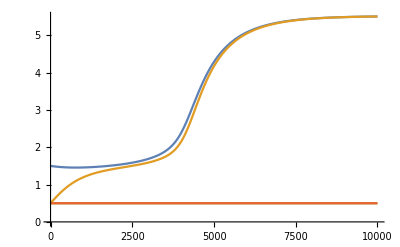

```mathematica
ListLinePlot[Transpose[numiterate]]
```

Now allow sex ratio traits to evolve:

```mathematica
numiterateSR=evol2equilibria[0.001,0.2,0.1,0.02,0.3,0.1,0.1,10000,Last[numiterate]];
```

{ym0→0.238806,ym1→0.0250742}

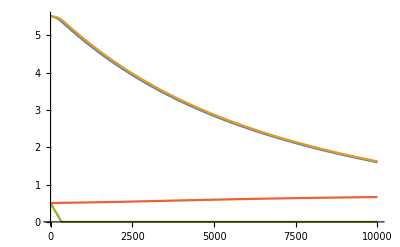

```mathematica
ListLinePlot[Transpose[numiterateSR]]
```